```mathematica
Off[NonlinearModelFit::cvmit,NIntegrate::ncvb,FindFit::cvmit,NonlinearModelFit::sszero]
```

Definition of Gauß, Lorentz, and Lorentz-transformed Lorentz functions

ILUM = (∫^∞)_e_th de 1/((σ_r-e)^2+σ_i^2)·1/((a_n-e)^2+b_n^2)

```mathematica
ClearAll;

ILnum[sr_,si_,a_,b_,eth_]:=NIntegrate[1/((sr-e)^2+si^2) 1/((a-e)^2+b^2),{e,eth,Infinity}]
ILana[sr_,si_,a_,b_,eth_,c_]:=c^1/(((sr-a)^2+(si-b)^2) ((sr-a)^2+(si+b)^2)) (((sr-a)^2+b^2-si^2)/si (Pi/2+ArcTan[(sr-eth)/si])+((sr-a)^2-b^2+si^2)/b (Pi/2+ArcTan[(a-eth)/b])+(sr-a) Log[((sr-eth)^2+si^2)/((a-eth)^2+b^2)])
Lorentz[e_,a_,b_,c_]:=c^1/((a-e)^2+b^2);
GaussX[x_,c_,a_,xo_]:=c Exp[-a (x-xo)^2];
```

Prepare cross-section and LIT data

i)    import cross section data
       datasets={“triton_inclusive_photo_abs.csv”,”compton_scattering_review_totProton.csv”,”compton_scattering_review_tot40Ca.csv”,”compton_scattering_review_tot16O.csv”,”compton_scattering_review_tot208Bi.csv”};
       
ii)  fit Gaussian basis to this data
iii) Lorentz-transform the expanded/interpolated data

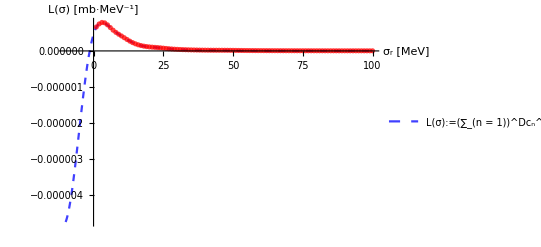

```mathematica
jj=0;
filen="~/kette_repo/ComptonLIT/av18_deuteron/real_LIT_J_"<>ToString[jj];


dataLIT=Import[filen,"Table","FieldSeparators"->" ; "];
guassdim=10;

modelGuass=Sum[GaussX[eGn,cGn@i,aGn@i,xoGn@i],{i,guassdim}];nlmG=NonlinearModelFit[dataLIT,modelGuass,Flatten[Table[{{cGn@i,0.1},{aGn@i,0.01},{xoGn@i,10.1}},{i,guassdim}],1],eGn];

modelLIT[s_]:=Sum[GaussX[s,cGn@i,aGn@i,xoGn@i],{i,guassdim}]/.nlmG["BestFitParameters"];

nbrS=100;
ub=100;
lb=-10;
sStellen=Range[lb,ub,(ub-lb)/nbrS];
si=5;
eth=2.1;

Show[
Plot[modelLIT[sr],{sr,lb,ub},PlotLegends->{"L(σ):=(∑_(n = 1))^Dc_n^*·e^(-SubsuperscriptBox[a, n, *] SuperscriptBox[(σ - SubsuperscriptBox[b, n, *]), 2])"},PlotRange->Full,AxesLabel->{"σ_r [MeV]","L(σ) [mb·MeV^-1]"},PlotStyle->{Blue,Thick,Dashed,Opacity[0.75]}],
ListPlot[dataLIT,PlotStyle->{Red,Opacity[0.75]}]
]
```

Determine appropriate (inspired) Lorentz parameters by fitting to the chosen set of cross-section data

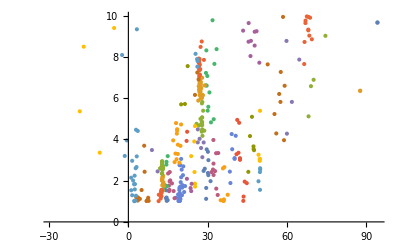

```mathematica
dataCross=Import["/home/kirscher/kette_repo/ComptonLIT/triton_inclusive_photo_abs.csv"];

desiredclusteranzahl=10;

inspireddimclustered=40;

inspireddim=180;
thup={100,10,100};
thlo={-1,1.0,10^-2};
tmpdim=0;
inspiredbas={};
While[tmpdim≤inspireddim,{

bassdim=8;

modelLorentzABC=Sum[ILana[srLn,si,aLn@i,bLn@i,eth,cLn@i],{i,bassdim}];

nlmLABC=NonlinearModelFit[dataCross,modelLorentzABC,Flatten[Table[{{aLn@i,RandomReal[{0.01,52.14}]},{bLn@i,RandomReal[{2.8,5.4}]},{cLn@i,RandomReal[{0.1,10.2}]}},{i,bassdim}],1],srLn];

basispara=Select[Table[{aLn@i,bLn@i,cLn@i},{i,bassdim}]/.nlmLABC["BestFitParameters"],Abs[#[[1]]]>thlo[[1]]&&Abs[#[[1]]]<thup[[1]]&&#[[2]]>thlo[[2]]&&Abs[#[[2]]]<thup[[2]]&&Abs[#[[3]]]>thlo[[3]]&&Abs[#[[3]]]<thup[[3]]&][[All,1;;2]];
If[Length[basispara]>0,AppendTo[inspiredbas,basispara]];
tmpdim=Length[inspiredbas];
}]
inspiredbas=Sort[Flatten[inspiredbas,1],#1[[1]]>#2[[1]]&];

tmp=FindClusters[inspiredbas,inspireddimclustered,Method->"KMedoids",DistanceFunction->EuclideanDistance][[All,1]];
ListPlot[FindClusters[inspiredbas,inspireddimclustered,Method->"KMedoids",DistanceFunction->EuclideanDistance]]
lorentzbas=tmp;
```

Adapt the inspired (see above)  chosen Lorentz-transformed Lorentz basis to the model LIT and compare the thereby reconstructed cross section with the original data

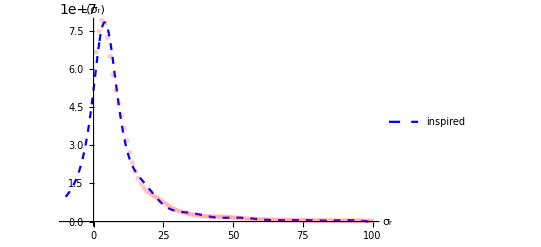

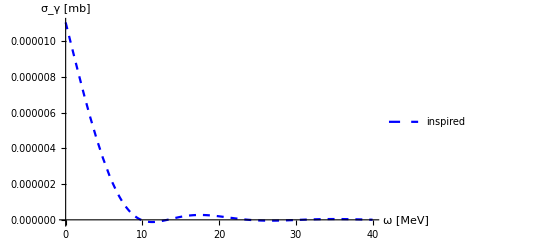

```mathematica
Clear[a];
lorentzbasinsp=FindClusters[Tuples[{lorentzbas[[All,1]],lorentzbas[[All,2]]}],desiredclusteranzahl,Method->"KMeans",DistanceFunction->EuclideanDistance][[All,1]];
(*BrayCurtisDistance,ChebyshevDistance*)
inspdim=Length[lorentzbasinsp];
coeffs=Array[a,inspdim];

LinearLorentzModel=Sum[ILana[sigmaR,si,lorentzbasinsp[[i]][[1]],lorentzbasinsp[[i]][[2]],eth,coeffs[[i]]],{i,inspdim}];
nlmL=FindFit[dataLIT,LinearLorentzModel,coeffs,sigmaR];

expan[x_]:=LinearLorentzModel/.nlmL/.sigmaR->x;

modelResponse[e_]:=(*HeavisideTheta[e-eth] *)Sum[Lorentz[e,lorentzbasinsp[[n]][[1]],lorentzbasinsp[[n]][[2]],coeffs[[n]]],{n,inspdim}]/.nlmL;

Show[
Plot[expan[x],{x,lb,ub},PlotLegends->{"inspired"},PlotRange->Full,AxesLabel->{"σ_r","L(σ_r)"},PlotStyle->{Blue,Dashed}],
ListPlot[dataLIT,PlotStyle->{Red,Opacity[0.2]},PlotLegends->"Gaussian LIT data"]
]
emin=0.0;emax=40;
Show[
Plot[{modelResponse[e]},{e,emin,emax},PlotRange->Full,PlotLegends->{"inspired"},AxesLabel->{"ω [MeV]","σ_γ [mb]"},PlotStyle->{{Blue,Dashed}}]
]
```

Adapt a randomly chosen Lorentz-transformed Lorentz basis to the model LIT and compare the thereby reconstructed cross section with the original data

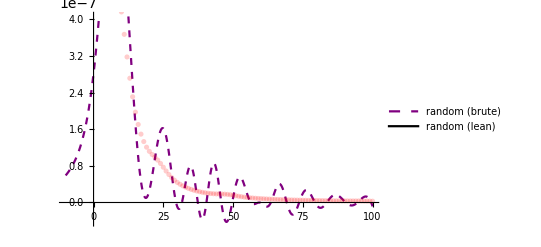

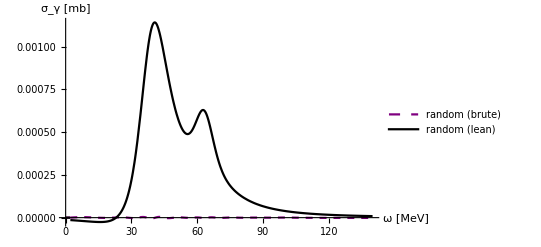

```mathematica
randdim=40;

lorentzCenters=RandomVariate[NormalDistribution[eth+50,25],randdim];
lorentzWidths=RandomVariate[NormalDistribution[10,2],randdim];

lorentzbasb=FindClusters[Tuples[{lorentzCenters,lorentzWidths}],desiredclusteranzahl,Method->"KMeans",DistanceFunction->CanberraDistance][[All,1]];
brutedim=Length[lorentzbasb];

constraintb=Table[1./((lorentzbasb[[n]][[1]]-eth)^2+lorentzbasb[[n]][[2]]^2),{n,brutedim}];

Clear[abrute];
coeffsb=Array[abrute,brutedim];

LinearLorentzModelb=Sum[ILana[sigmaR,si,lorentzbasb[[i]][[1]],lorentzbasb[[i]][[2]],eth,coeffsb[[i]]],{i,brutedim}];
nlmLb=FindFit[dataLIT,{LinearLorentzModelb,Abs[coeffsb.constraintb]<10^-4},coeffsb,sigmaR];
Values[nlmLb].constraintb;

expanb[x_]:=LinearLorentzModelb/.nlmLb/.sigmaR->x;
modelResponseb[e_]:=HeavisideTheta[e-eth] Sum[Lorentz[e,lorentzbasb[[n]][[1]],lorentzbasb[[n]][[2]],coeffsb[[n]]],{n,brutedim}]/.nlmLb;

goodBVs=Position[Values[nlmLb],_?(Abs[#]>10^-1&)];
nlmLblean=Extract[nlmLb,goodBVs];
lorentzbasblean=Extract[lorentzbasb,goodBVs];
LeanLorentzModelb=Sum[ILana[sigmaR,si,lorentzbasblean[[i]][[1]],lorentzbasblean[[i]][[2]],eth,coeffsb[[goodBVs[[i]]]]],{i,Length[lorentzbasblean]}];

expanblean[x_]:=LeanLorentzModelb/.nlmLblean/.sigmaR->x;

modelResponseblean[e_]:=HeavisideTheta[e-eth] Sum[Lorentz[e,lorentzbasblean[[n]][[1]],lorentzbasblean[[n]][[2]],coeffsb[[goodBVs[[n]]]]],{n,Length[lorentzbasblean]}]/.nlmLblean;

Show[
Plot[expanb[x],{x,lb,ub},PlotStyle->{Purple,Thick,Dashed},PlotLegends->{"random (brute)"}],
Plot[expanblean[x],{x,lb,ub},PlotStyle->{Black},PlotLegends->{"random (lean)"}],
ListPlot[dataLIT,PlotStyle->{Red,Opacity[0.2]},PlotLegends->"Gaussian LIT data"]
]
emin=0.0;emax=140;
Show[
Plot[{modelResponseb[e],modelResponseblean[e]},{e,emin,emax},PlotRange->Full,PlotLegends->{"random (brute)","random (lean)"},AxesLabel->{"ω [MeV]","σ_γ [mb]"},PlotStyle->{{Purple,Dashed,Thick},{Black}}]
]
```